# Causal Structure in X direction

```mathematica
c=3 10^8 ;
```

## Events

```mathematica
e1 = {2 10^-6 c, 300,0,0}; e2 = {3 10^-6 c, 500,0,0};
```

## Square of the spacetime interval

```mathematica
SquareInterval[ev1_,ev2_]:=(ev2[[1]]-ev1[[1]])^2-(ev2[[2]]-ev1[[2]])^2-(ev2[[3]]-ev1[[3]])^2-(ev2[[4]]-ev1[[4]])^2
```

```mathematica
SquareInterval[e1,e2]
```

50000

## Diagram

```mathematica
p1=Plot[x,{x,0,1000},AxesLabel->{"x","c t"},PlotStyle->Red,AspectRatio->Automatic];
```

```mathematica
p2=ListPlot[{{e1[[2]],e1[[1]]},{e2[[2]],e2[[1]]}},Joined->True,MeshStyle->Red,PlotMarkers->{Automatic,Medium}];
```

```mathematica
e1text=Graphics[{Red,Text["Event 1",{0,30}+{e1[[2]],e1[[1]]}]}];
```

```mathematica
e2text=Graphics[{Red,Text["Event 2",{0,30}+{e2[[2]],e2[[1]]}]}];
```

```mathematica
p3=Graphics[{Thickness[Small],Dashed,Pink,Line[{{e1[[2]],0},{e1[[2]],e1[[1]]}}]}];
```

```mathematica
p4=Graphics[{Thickness[Small],Dashed,Pink,Line[{{0,e1[[1]]},{e1[[2]],e1[[1]]}}]}];
```

```mathematica
p5=Graphics[{Thickness[Small],Dashed,Pink,Line[{{e2[[2]],0},{e2[[2]],e2[[1]]}}]}];
```

```mathematica
p6=Graphics[{Thickness[Small],Dashed,Pink,Line[{{0,e2[[1]]},{e2[[2]],e2[[1]]}}]}];
```

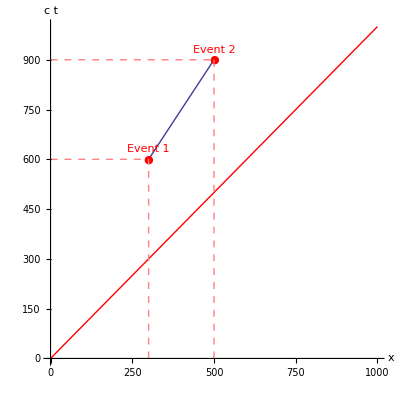

```mathematica
Show[p1,p2,p3,p4,p5,p6,e1text,e2text]
```

## Causal Structure

```mathematica
CausalStructure[ev1_,ev2_]:=If[SquareInterval[ev1,ev2]>0,Print["Time-like interval"],If[SquareInterval[ev1,ev2]<0,Print["Space-like interval"],Print["Light-like interval"]]]
```

```mathematica
CausalStructure[e1,e2]
```

Time-like interval

## Δx/Δt

```mathematica
Δx[ev1_,ev2_]:=ev2[[2]]-ev1[[2]]
```

```mathematica
Δx[e1,e2]
```

200

```mathematica
Δt[ev1_,ev2_]:=(ev2[[1]]-ev1[[1]])/c
```

```mathematica
Δt[e1,e2]
```

1/1000000

```mathematica
Δx[e1,e2]/Δt[e1,e2]
```

200000000

## Lorentz transformation

```mathematica
v=0.8c;
```

```mathematica
Subscript[Λ, x]=({{γ, -β γ, 0, 0}, {-β γ, γ, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})/.γ->1/(√(1-β^2))/.β->v/c;
```

```mathematica
SquareInterval[Subscript[Λ, x].e1,Subscript[Λ, x].e2]//FullSimplify
```

50000.

Spacetime interval is invariant :

```mathematica
SquareInterval[Subscript[Λ, x].e1,Subscript[Λ, x].e2]==SquareInterval[e1,e2]//FullSimplify
```

True